Code for the article "Translational and great Darboux cyclides" by Niels Lubbes .  We use the notation and definitions from the article .

## Euclidean translations

We verify that Euclidean translations of the projective 3-sphere are indeed Moebius transformations and correspond via the stereographic projection to translations of Euclidean 3-space.

```mathematica
Remove["Global`*"]
mat={{2+y1^2+y2^2+y3^2,2*y1,2*y2,2*y3,-y1^2-y2^2-y3^2},{2*y1,2,0,0,-2*y1},{2*y2,0,2,0,-2*y2},{2*y3,0,0,2,-2*y3},{y1^2+y2^2+y3^2,2*y1,2*y2,2*y3,2-y1^2-y2^2-y3^2}};
(* check that mat defines a Moebius transformation *)
J=DiagonalMatrix[{-1,1,1,1,1}];
Expand[Transpose[mat].J.mat]==4*J 
(* Check that mat corresponds to an Euclidean translation. *)
sp[x_]:={x[[1]]-x[[5]],x[[2]],x[[3]],x[[4]]}; (* stereographic projection *)
Expand[sp[mat.{x0,x1,x2,x3,0}]/2]
```

True

{x0,x1+x0 y1,x2+x0 y2,x3+x0 y3}

## Initialization of classes and real involutions

We intialize the classes, the intersection matrix, the matrices corresponding to the involutions 2A1, 3A1 and D4 that are induced by the real structure. We also initialize a list with all possible B(X) together with the corresponding name and involutions.

```mathematica
(* Define notation for the classes in the sets B(X), E(X) and G(X). *)
(*declare classes in E(X)*)
e1={0,0,1,0,0,0};
e2={0,0,0,1,0,0};
e3={0,0,0,0,1,0};
e4={0,0,0,0,0,1};
e01={1,0,-1,0,0,0};
e02={1,0,0,-1,0,0};
e03={1,0,0,0,-1,0};
e04={1,0,0,0,0,-1};
e11={0,1,-1,0,0,0};
e12={0,1,0,-1,0,0};
e13={0,1,0,0,-1,0};
e14={0,1,0,0,0,-1};
ep1={1,1,0,-1,-1,-1};
ep2={1,1,-1,0,-1,-1};
ep3={1,1,-1,-1,0,-1};
ep4={1,1,-1,-1,-1,0};
(*declare classes in G(X)*)
g0={1,0,0,0,0,0};
g1={0,1,0,0,0,0};
g2={2,1,-1,-1,-1,-1};
g3={1,2,-1,-1,-1,-1};
g12={1,1,-1,-1,0,0};
g34={1,1,0,0,-1,-1};
g13={1,1,-1,0,-1,0};
g24={1,1,0,-1,0,-1};
g14={1,1,-1,0,0,-1};
g23={1,1,0,-1,-1,0};
(*declare classes in B(X)*)
b12={1,0,-1,-1,0,0};
b13={1,0,-1,0,-1,0};
b24={1,0,0,-1,0,-1};
b34={1,0,0,0,-1,-1};
bp12={0,1,-1,-1,0,0};
bp13={0,1,-1,0,-1,0};
bp14={0,1,-1,0,0,-1};
bp23={0,1,0,-1,-1,0};
bp24={0,1,0,-1,0,-1};
bp34={0,1,0,0,-1,-1};
b0={1,1,-1,-1,-1,-1};
b1={0,0,1,0,-1,0};
b2={0,0,0,1,0,-1};

(* The following symmetric matrix defines the quadratic form for the intersection product between classes. *)
M={{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,-1,0,0,0},
{0,0,0,-1,0,0},{0,0,0,0,-1,0},{0,0,0,0,0,-1}};

(* The following three matrices define the real structures of type 2A1, 3A1 and D4 (see Section 4). *)
rs2A1={{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0}};
rs3A1={{0,1,0,0,0,0},{1,0,0,0,0,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0}};
rsD4={{1,0,0,0,0,0},{2,1,1,1,1,1},{-1,0,-1,0,0,0},{-1,0,0,-1,0,0},{-1,0,0,0,-1,0},{-1,0,0,0,0,-1}};

(* Converts class or real structure to string. *)
str[q_]:=Module[{},
If[q==e1,Return["e1"]];
If[q==e2,Return["e2"]];
If[q==e3,Return["e3"]];
If[q==e4,Return["e4"]];
If[q==e01,Return["e01"]];
If[q==e02,Return["e02"]];
If[q==e03,Return["e03"]];
If[q==e04,Return["e04"]];
If[q==e11,Return["e11"]];
If[q==e12,Return["e12"]];
If[q==e13,Return["e13"]];
If[q==e14,Return["e14"]];
If[q==ep1,Return["ep1"]];
If[q==ep2,Return["ep2"]];
If[q==ep3,Return["ep3"]];
If[q==ep4,Return["ep4"]];
If[q==g0,Return["g0"]];
If[q==g1,Return["g1"]];
If[q==g12,Return["g12"]];
If[q==g34,Return["g34"]];
If[q==g2,Return["g2"]];
If[q==g3,Return["g3"]];
If[q==g13,Return["g13"]];
If[q==g24,Return["g24"]];
If[q==g14,Return["g14"]];
If[q==g23,Return["g23"]];
If[q==b12,Return["b12"]];
If[q==b13,Return["b13"]];
If[q==b24,Return["b24"]];
If[q==b34,Return["b34"]];
If[q==bp12,Return["bp12"]];
If[q==bp13,Return["bp13"]];
If[q==bp14,Return["bp14"]];
If[q==bp23,Return["bp23"]];
If[q==bp24,Return["bp24"]];
If[q==bp34,Return["bp34"]];
If[q==b0,Return["b0"]];
If[q==b1,Return["b1"]];
If[q==b2,Return["b2"]];
If[q==rs2A1,Return["rs2A1"]];
If[q==rs3A1,Return["rs3A1"]];
If[q==rsD4,Return["rsD4"]];
If[q!=Flatten[q],Return@ToString[str/@q]]; (* apply recursively str to each element in the list q *)
Return[ToString[q]]
];

(* All possible elements of E(X), G(X) and B(X). *)
allEX= {e1,e2,e3,e4,e01,e02,e03,e04,e11,e12,e13,e14,ep1,ep2,ep3,ep4};
allGX={g0,g1,g2,g3,g12,g13,g14,g23,g24,g34};
allBX={b12,b13,b24,b34,bp12,bp13,bp14,bp23,bp24,bp34,b0,b1,b2};

(* The set B(X) for each row of Table 3 in Section 4. *)
(* rs2A1 *)
Blum={};
Perseus={b1,b2};
Ring={b13,b24,bp14,bp23};
EH1={b12};
CH1={b13,b24,bp12};
HP={b12,bp34};
EY={b12,b1,b2};
CY={b12,b1,b2,bp13,bp24};
EO={b12,b34};
CO={b12,b34,bp13,bp24};
(* rs3A1 *)
EEorEH2={b0};
EP={b13,bp24};
S1={};
(* rsD4 *)
S2={};

(*List of possible B(X) together with name and real structure.*)
classBX={
{"Blum",Blum,rs2A1},
{"Perseus",Perseus,rs2A1},
{"Ring",Ring,rs2A1},
{"EH1",EH1,rs2A1},
{"CH1",CH1,rs2A1},
{"HP",HP,rs2A1},
{"EY",EY,rs2A1},
{"CY",CY,rs2A1},
{"EO",EO,rs2A1},
{"CO",CO,rs2A1},
{"EE/EH2",EEorEH2,rs3A1},
{"EP",EP,rs3A1},
{"S1",S1,rs3A1},
{"S2",S2,rsD4}
};
```

```mathematica
(* The real structures act on the classes as follows. *)
bas={g0,g1,e1,e2,e3,e4};
Print["2A1"];
inv[q_]:=rs2A1.q;{str/@bas,str/@inv/@bas}//TableForm
Print["3A1"];
inv[q_]:=rs3A1.q;{str/@bas,str/@inv/@bas}//TableForm
Print["D4"];inv[q_]:=rsD4.q;{str/@bas,str/@inv/@bas}//TableForm
```

2A1

g0 | g1 | e1 | e2 | e3 | e4
g0 | g1 | e2 | e1 | e4 | e3

3A1

g0 | g1 | e1 | e2 | e3 | e4
g1 | g0 | e2 | e1 | e4 | e3

D4

g0 | g1 | e1 | e2 | e3 | e4
g3 | g1 | e11 | e12 | e13 | e14

```mathematica
(* Pretty print the table `classBX`. *)
TableForm@Table[{classBX[[i,1]],str@classBX[[i,2]],str@classBX[[i,3]]},{i,1,Length[classBX]}]
```

Blum | {} | rs2A1
Perseus | {b1, b2} | rs2A1
Ring | {b13, b24, bp14, bp23} | rs2A1
EH1 | {b12} | rs2A1
CH1 | {b13, b24, bp12} | rs2A1
HP | {b12, bp34} | rs2A1
EY | {b12, b1, b2} | rs2A1
CY | {b12, b1, b2, bp13, bp24} | rs2A1
EO | {b12, b34} | rs2A1
CO | {b12, b34, bp13, bp24} | rs2A1
EE/EH2 | {b0} | rs3A1
EP | {b13, bp24} | rs3A1
S1 | {} | rs3A1
S2 | {} | rsD4

```mathematica
(* We print a table that specifies the intersection products between elements in B(X) and G(X)&E(X). *)
allGEX=allGX~Join~allEX;
tab=Table[allBX[[i]].M.allGEX[[j]],{i,1,Length[allBX]},{j,1,Length[allGEX]}];
TableForm@({{x}~Join~(str/@allGEX)}~Join~Transpose[{str/@allBX}~Join~Transpose@tab]) (* display table with column and row headers *)
```

x | g0 | g1 | g2 | g3 | g12 | g13 | g14 | g23 | g24 | g34 | e1 | e2 | e3 | e4 | e01 | e02 | e03 | e04 | e11 | e12 | e13 | e14 | ep1 | ep2 | ep3 | ep4
b12 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | -1
b13 | 0 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | -1
b24 | 0 | 1 | -1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | -1 | 1 | 0 | 1 | 0 | -1 | 0 | -1 | 0
b34 | 0 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | -1 | 1 | 1 | 0 | 0 | -1 | -1 | 0 | 0
bp12 | 1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1
bp13 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | -1
bp14 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | -1 | 0
bp23 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | -1
bp24 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | -1 | 0
bp34 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0
b0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1
b1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | -1 | -1 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 1 | 0
b2 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 1

## Tables 3 and 4

```mathematica
(* 
The input `BX` represents the list B(X). The output is the list E(X) and corresponds to the elements in `allEX` that are non-negative with respect to each element in B(X).
*)
getEX[BX_]:=Return@Select[allEX, 
AllTrue[Table[#.M.BX [[i]],{i,Length[BX]}],NonNegative]&
];

(*
The input `BX` represents the list B(X).The output is the list G(X) and corresponds to the elements in `allGX` that are non-negative with respect to each element in B(X).
*)
getGX[BX_]:=Return@Select[allGX,
AllTrue[Table[#.M.BX[[i]],{i,Length[BX]}],NonNegative]&
];

(*
The input `lst is a list of classes and `rs` is the real structure `rs2A1`, `rs3A1` or `rsD4`. The output consist of the elements in "lst" that are real.
*)
getReal[lst_,rs_]:=Return@Select[lst,rs.#==#&];

(* 
Takes as input a list BX corresponding to B(X) and outputs a list of components in B(X), which is a sub list. See Section 4 for the definition of component.
*)
getComponents[BX_, clst_:{}]:=Module[{comp},
If[Length[BX]==0, Return[clst]];
comp=Select[BX,#.M.First[BX]!=0&];
Return@getComponents[ Complement[BX,comp],clst~Join~{comp}]
];
```

```mathematica
(*
We apply for each element in `classBX`.
*)
Print["E(X)\n---"]
Grid[Table[{classBX[[i,1]],str@getEX[classBX[[i,2]]]},
{i,1,Length[classBX]}],Alignment->Left]
Print["G(X) and real elements of G(X)\n---"]
Grid[Table[{classBX[[i,1]],str@getGX[classBX[[i,2]]],str@getReal[getGX[classBX[[i,2]]],classBX[[i,3]]]},
{i,1,Length[classBX]}],Alignment->Left]
Print["Components of B(X)\n---"]
Grid[Table[{classBX[[i,1]]}~Join~Map[str,getComponents[classBX[[i,2]]],{2}],
{i,1,Length[classBX]}],Alignment->Left]
```

E(X)
---

Blum | {e1, e2, e3, e4, e01, e02, e03, e04, e11, e12, e13, e14, ep1, ep2, ep3, ep4}
Perseus | {e3, e4, e01, e02, e11, e12, ep3, ep4}
Ring | {e1, e2, e3, e4}
EH1 | {e1, e2, e3, e4, e03, e04, e11, e12, e13, e14, ep1, ep2}
CH1 | {e1, e2, e3, e4, e13, e14}
HP | {e1, e2, e3, e4, e03, e04, e11, e12}
EY | {e3, e4, e11, e12}
CY | {e3, e4}
EO | {e1, e2, e3, e4, e11, e12, e13, e14}
CO | {e1, e2, e3, e4}
EE/EH2 | {e1, e2, e3, e4, e01, e02, e03, e04, e11, e12, e13, e14}
EP | {e1, e2, e3, e4, e02, e04, e11, e13}
S1 | {e1, e2, e3, e4, e01, e02, e03, e04, e11, e12, e13, e14, ep1, ep2, ep3, ep4}
S2 | {e1, e2, e3, e4, e01, e02, e03, e04, e11, e12, e13, e14, ep1, ep2, ep3, ep4}

G(X) and real elements of G(X)
---

Blum | {g0, g1, g2, g3, g12, g13, g14, g23, g24, g34} | {g0, g1, g2, g3, g12, g34}
Perseus | {g0, g1, g2, g3, g12, g13, g24} | {g0, g1, g2, g3, g12}
Ring | {g0, g1, g12, g34} | {g0, g1, g12, g34}
EH1 | {g0, g1, g3, g13, g14, g23, g24, g34} | {g0, g1, g3, g34}
CH1 | {g0, g1, g14, g23, g34} | {g0, g1, g34}
HP | {g0, g1, g13, g14, g23, g24} | {g0, g1}
EY | {g0, g1, g3, g13, g24} | {g0, g1, g3}
CY | {g0, g1} | {g0, g1}
EO | {g0, g1, g3, g13, g14, g23, g24} | {g0, g1, g3}
CO | {g0, g1, g14, g23} | {g0, g1}
EE/EH2 | {g0, g1, g12, g13, g14, g23, g24, g34} | {g12, g34}
EP | {g0, g1, g12, g14, g23, g34} | {g12, g34}
S1 | {g0, g1, g2, g3, g12, g13, g14, g23, g24, g34} | {g12, g34}
S2 | {g0, g1, g2, g3, g12, g13, g14, g23, g24, g34} | {g1, g2}

Components of B(X)
---

Blum |  |  |  | 
Perseus | {b1} | {b2} |  | 
Ring | {b13} | {bp14} | {bp23} | {b24}
EH1 | {b12} |  |  | 
CH1 | {b13} | {bp12} | {b24} | 
HP | {b12,bp34} |  |  | 
EY | {b12,b1,b2} |  |  | 
CY | {b12,b1,b2} | {bp13} | {bp24} | 
EO | {b12} | {b34} |  | 
CO | {b12} | {bp13} | {bp24} | {b34}
EE/EH2 | {b0} |  |  | 
EP | {b13,bp24} |  |  | 
S1 |  |  |  | 
S2 |  |  |  |

## Example 9

```mathematica
(*
The inputs `u` is either a class or a component of B(X). If `u` is a class, then we replace it with a list `{u}`.Similarly, for the input `v`. We consider the set {a.M.b : a in u, b in v} of all possible products of classes in the lists u and v. If this set contains a negative element, then we return -1 and the maximum of this set otherwise. 
*)
mult[u_,v_]:=Module[{set},
If[Flatten[u]==u,Return@mult[{u},v]];
If[Flatten[v]==v,Return@mult[u,{v}]];
set=Flatten@Table[u[[i]].M.v[[j]],{i,Length[u]},{j,Length[v]}];
If[Min@set<0, Return[-1],Return@Max@set];
];
```

```mathematica
(* Test the function mult[] *)
W={b12,b1,b2};
{mult[W,e1],mult[e1,W],mult[e3,W],mult[g0,e12],mult[W,W],mult[e1,e2]}
```

{-1,-1,1,1,-1,0}

For each entry of the classification table `classBX` we construct a graph whose vertices correspond to classes in E (X) and components in B (X) . There is an edge between vertices u and v if and only if `mult[u, v] == 1`.

From this graph we can recover the diagram in Example 9 as follows . We replace each vertex in E (X) with a line segment . Two line segments are either disjoint or meet at no more than one disc . The line segments corresponding to vertices u and v in E (X) meet at a disc iff one of the following two cases holds : 

(1) If {u, W} and {v, W} are edges for some vertex W that is a component, then the line segments corresponding to u and v meet at a disc labeled with the sum of elements in W . 

(2) If {u, v} is an edge and {u, W} is not an edge for all vertices W that are components, then the line segments meet at an unlabeled disc .

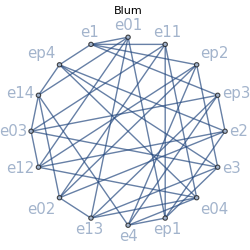
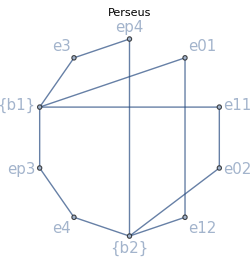
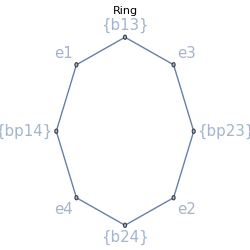
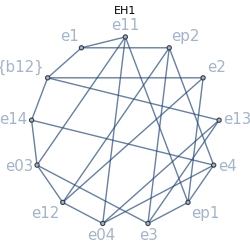
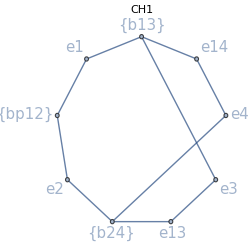
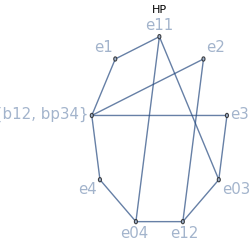
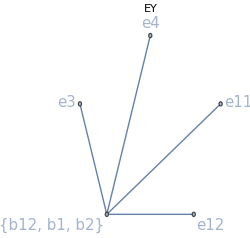
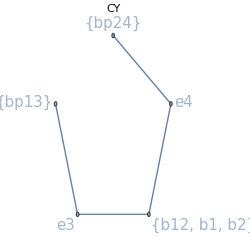
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
lst={};
For[i=1,i<=Length[classBX],i++,
(* initialize data from entry classBX[[i]] *)
{name, BX,rs}=classBX[[i]];

(* the vertices of the adjacency graph is the union of E(X) and the components in B(X)*)
vert=getEX[BX]~Join~getComponents[BX]; 

(* construct adjacency matrix using mult[] *)
adj=Table[mult[vert[[i]],vert[[j]]],{i,Length[vert]},{j,Length[vert]}];
adj=Map[Max[0,#]&,adj ,{2}]; (* replace negative entries with 0 *)

(* create adjacency graph and add to list *)
ag=GraphPlot[AdjacencyGraph[adj,VertexLabels->Table[i->str@vert[[i]],{i,Length[vert]}],ImageSize->250,PlotLabel->name,GraphLayout->"CircularEmbedding"],PlotStyle->{FontSize->15}];
lst=lst~Join~{ag};
];
TableForm@Partition[lst,UpTo[4]]
Export["adjacency-graphs-cyclides.png",TableForm@Partition[lst,UpTo[4]]];
```

## Example 10

```mathematica
str@Ring (* B(X) for the ring cyclide *)
str@getReal[getGX[Ring],rs2A1] (* get the real classes in G(X)*)
{g12.M.g34,g0.M.g1}=={2,1} (* g12 and g34 correspond to the families of Villarceau circles as they intersect in two points *)
{mult[g0,bp14],mult[g0,bp23],mult[g1,b13],mult[g1,b24]}=={1,1,1,1} (* g0 and g1 have each two base points *)
{rs2A1.bp13,rs2A1.bp14}=={bp24,bp23} (* bp13 and bp14 are complex conjugate to bp24 and bp23, respectively *)
```

{b13, b24, bp14, bp23}

{g0, g1, g12, g34}

True

True

True

## Lemma 11

```mathematica
(* The inputs `W` and `rs` represent a component of B(X) and the real structure,respectively. The output is True if the component is send to itself by the real structure. *)
isRealComp[W_,rs_]:=Return[Sort@Map[rs.#&,W]==Sort@W]
```

```mathematica
(* Lemma 11[a,b]: Go through the classification and find real classes g in G(X) and complex components W in B(X) such that mult[g,W]>0 *)
For[i=1,i<=Length[classBX],i++,
{name,BX,rs}=classBX[[i]];
RGX=getReal[getGX[BX],rs]; (* real classes in GX *)
cc=Select[getComponents[BX], !isRealComp[#,rs]&]; (* complex components in B(X) *)
tab=Table[{mult[RGX[[i]],cc[[j]]],str@RGX[[i]],str@cc[[j]]},
{i,Length[RGX]},{j,Length[cc]}];
tab=Flatten[tab,1];
If[tab!={},Print[name,": ",Select[tab,#[[1]]>0&]]];
];
```

Perseus: {{1,g12,{b1}},{1,g12,{b2}}}

Ring: {{1,g0,{bp14}},{1,g0,{bp23}},{1,g1,{b13}},{1,g1,{b24}}}

CH1: {{1,g1,{b13}},{1,g1,{b24}}}

CY: {{1,g0,{bp13}},{1,g0,{bp24}}}

CO: {{1,g0,{bp13}},{1,g0,{bp24}}}

```mathematica
(* Lemma 11c *)
(* CY *)
{W}=Select[getComponents[CY],isRealComp[#,rs2A1]&];
EX=getEX[CY];
{str@W,str@EX}
{mult[W,e3],mult[W,e4]}=={1,1}

(* CO *)
{W1,W2}=Select[getComponents[CO],isRealComp[#,rs2A1]&];
EX=getEX[CO];
{str@W1,str@W2,str@EX}
{mult[W1,e1],mult[W1,e2],mult[W2,e3],mult[W2,e4]}=={1,1,1,1}
```

{{b12, b1, b2},{e3, e4}}

True

{{b12},{b34},{e1, e2, e3, e4}}

True

## Example 16 and Proposition 19

```mathematica
(* 
The input `u` and `v` are classes and `BX` corresponds to the set B(X). We assume that `mult[W,u]>=0' and 'mult[W,v]>=0' for all components W in B(X).
The output is the odot multiplication as defined in Section 5. 
*)
odot[u_,v_,BX_]:=Module[{compList,tab},
compList = getComponents[BX];
If[mult[u,v]>0,Return[1]];
tab=Table[ mult[compList[[i]],u]*mult[compList[[i]],v],{i,Length[compList]}];
If[Min@tab<0, Return[0]];
If[Max@tab>0,Return[1]];
Return[0];
];

(* The inputs `q1`, `q2`, `q3` and `q4` represent classes, the input `BX` represent the set B(X), and `rs` is the real structure.
The output is `True` if the four classes form a Clifford quartet and `False` otherwise. *)
isQuartet[a_,b_,c_,d_,BX_,rs_]:=
If[rs.a==b &&rs.c==d &&
odot[a,b,BX]==0 && odot[c,d,BX]==0 &&
odot[a,c,BX]==1 && odot[c,b,BX]==1 &&
odot[b,d,BX]==1 && odot[d,a,BX]==1,
Return[True],(* else *) Return[False]];

(* The inputs `e` and `a` are classes, `A` is a list of four classes {a,b,c,d} containing `a` and `BX` represents B(X). 
Returns `True` if the class e belongs to U as defined at Definition 15. *)
inU[e_,A_,a_,BX_]:=Module[{b,c,d},
{b,c,d}=Select[A,#!=a&];
Return[{e.M.a,odot[e,b,BX],odot[e,c,BX],odot[e,d,BX]}=={1,0,0,0}];
];

(* Verifies whether there exists g in T such that g.M.u!=0 for all u in U. *)
check[T_,U_]:=Module[{i},
For[i=1,i≤Length[T],i++,
If[ !MemberQ[Map[#.M.T[[i]]&,U],0],Return[True]];
];
Return[False];
];

(* 
The input `BX` and `rs` represent B(X) and the real structure, respectively.
This method prints a list of all tuples (A,a,T,U) that satisfy the following property: 
(A,a,g,U) is a Clifford data if and only if g in T. 
For each such tuple we print True if and only if there exists g in T such that the Clifford data (A,a,g,U) is a certificate for the Clifford criterion (see Section 5).
*)
printCliffordData[BX_,rs_]:=Module[{EX,RGX,Q,i,j,A,a,T,U},
(* initialize E(X) and the subset of real classes in G(X)*)
EX=getEX[BX];
RGX=getReal[getGX[BX],rs];

(* We compute a list of all Clifford quartets, using exhaustive search *)
Q=DeleteDuplicatesBy[Sort]@
Select[Permutations[EX,{4}],isQuartet[#[[1]],#[[2]],#[[3]],#[[4]],BX,rs]&]; 
If[Length[Q]==0, Print["There exist no Clifford quartets."]];

(* We compute all tuples (A,a,T,U) *)
For[i=1,i<=Length[Q],i++,
For[j=1,j≤4,j++,
A=Q[[i]];a=Q[[i,j]];
T=Select[RGX,#.M.a>0&];
U=Select[EX,inU[#,A,a,BX]&];
Print[str@A," ",str[a]," ",str@T," ",str@U," "," Certificate for Clifford criterion: "<>ToString[check[T,U]]];
];
];
];
```

```mathematica
(*
Print all Clifford data that are candidates for certificates for the Clifford criterion. 
*)
For[i = 1, i <= Length[classBX], i++,
  {name, BX, rs} = classBX[[i]];
  Print["\n" <> name <> "\n-------"];
  printCliffordData[BX, rs];
  ];
```

Blum
-------

{e1, e2, ep3, ep4} e1 {g2, g3, g12} {e01, e11, ep2}  Certificate for Clifford criterion: False

{e1, e2, ep3, ep4} e2 {g2, g3, g12} {e02, e12, ep1}  Certificate for Clifford criterion: False

{e1, e2, ep3, ep4} ep3 {g0, g1, g34} {e4, e03, e13}  Certificate for Clifford criterion: False

{e1, e2, ep3, ep4} ep4 {g0, g1, g34} {e3, e04, e14}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} e3 {g2, g3, g34} {e03, e13, ep4}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} e4 {g2, g3, g34} {e04, e14, ep3}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} ep1 {g0, g1, g12} {e2, e01, e11}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} ep2 {g0, g1, g12} {e1, e02, e12}  Certificate for Clifford criterion: False

{e01, e02, e13, e14} e01 {g1, g3, g34} {e1, e12, ep1}  Certificate for Clifford criterion: False

{e01, e02, e13, e14} e02 {g1, g3, g34} {e2, e11, ep2}  Certificate for Clifford criterion: False

{e01, e02, e13, e14} e13 {g0, g2, g12} {e3, e04, ep3}  Certificate for Clifford criterion: False

{e01, e02, e13, e14} e14 {g0, g2, g12} {e4, e03, ep4}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e03 {g1, g3, g12} {e3, e14, ep3}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e04 {g1, g3, g12} {e4, e13, ep4}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e11 {g0, g2, g34} {e1, e02, ep1}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e12 {g0, g2, g34} {e2, e01, ep2}  Certificate for Clifford criterion: False

Perseus
-------

{e3, e4, ep3, ep4} e3 {g2, g3} {}  Certificate for Clifford criterion: True

{e3, e4, ep3, ep4} e4 {g2, g3} {}  Certificate for Clifford criterion: True

{e3, e4, ep3, ep4} ep3 {g0, g1} {}  Certificate for Clifford criterion: True

{e3, e4, ep3, ep4} ep4 {g0, g1} {}  Certificate for Clifford criterion: True

{e01, e02, e11, e12} e01 {g1, g3} {}  Certificate for Clifford criterion: True

{e01, e02, e11, e12} e02 {g1, g3} {}  Certificate for Clifford criterion: True

{e01, e02, e11, e12} e11 {g0, g2} {}  Certificate for Clifford criterion: True

{e01, e02, e11, e12} e12 {g0, g2} {}  Certificate for Clifford criterion: True

Ring
-------

{e1, e2, e3, e4} e1 {g12} {}  Certificate for Clifford criterion: True

{e1, e2, e3, e4} e2 {g12} {}  Certificate for Clifford criterion: True

{e1, e2, e3, e4} e3 {g34} {}  Certificate for Clifford criterion: True

{e1, e2, e3, e4} e4 {g34} {}  Certificate for Clifford criterion: True

EH1
-------

{e3, e4, ep1, ep2} e3 {g3, g34} {e03, e13}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} e4 {g3, g34} {e04, e14}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} ep1 {g0, g1} {e2, e11}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} ep2 {g0, g1} {e1, e12}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e03 {g1, g3} {e3, e14}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e04 {g1, g3} {e4, e13}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e11 {g0, g34} {e1, ep1}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e12 {g0, g34} {e2, ep2}  Certificate for Clifford criterion: False

CH1
-------

{e3, e4, e13, e14} e3 {g34} {}  Certificate for Clifford criterion: True

{e3, e4, e13, e14} e4 {g34} {}  Certificate for Clifford criterion: True

{e3, e4, e13, e14} e13 {g0} {}  Certificate for Clifford criterion: True

{e3, e4, e13, e14} e14 {g0} {}  Certificate for Clifford criterion: True

HP
-------

{e03, e04, e11, e12} e03 {g1} {e3}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e04 {g1} {e4}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e11 {g0} {e1}  Certificate for Clifford criterion: False

{e03, e04, e11, e12} e12 {g0} {e2}  Certificate for Clifford criterion: False

EY
-------

There exist no Clifford quartets.

CY
-------

There exist no Clifford quartets.

EO
-------

There exist no Clifford quartets.

CO
-------

There exist no Clifford quartets.

EE/EH2
-------

There exist no Clifford quartets.

EP
-------

There exist no Clifford quartets.

S1
-------

{e1, e2, ep3, ep4} e1 {g12} {e01, e11, ep2}  Certificate for Clifford criterion: False

{e1, e2, ep3, ep4} e2 {g12} {e02, e12, ep1}  Certificate for Clifford criterion: False

{e1, e2, ep3, ep4} ep3 {g34} {e4, e03, e13}  Certificate for Clifford criterion: False

{e1, e2, ep3, ep4} ep4 {g34} {e3, e04, e14}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} e3 {g34} {e03, e13, ep4}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} e4 {g34} {e04, e14, ep3}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} ep1 {g12} {e2, e01, e11}  Certificate for Clifford criterion: False

{e3, e4, ep1, ep2} ep2 {g12} {e1, e02, e12}  Certificate for Clifford criterion: False

S2
-------

There exist no Clifford quartets.

## Example 20

```mathematica
(* Matrices corresponding to Moebius transformations *)
M0={{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
M1={{5,0,0,0,0},{0,5,0,0,0},{0,0,4,-3,0},{0,0,3,4,0},{0,0,0,0,5}};
M2={{3,0,0,-2,-2},{0,1,0,0,0},{0,0,1,0,0},{-2,0,0,1,2},{2,0,0,-2,-1}};
M3={{3,0,0,2,-1},{0,2,0,0,0},{0,0,2,0,0},{2,0,0,2,-2},{1,0,0,2,1}};
M4={{3,-2,0,0,-1},{-2,2,0,0,2},{0,0,2,0,0},{0,0,0,2,0},{1,-2,0,0,1}};
M5={{3,2,0,0,-1},{2,2,0,0,-2},{0,0,2,0,0},{0,0,0,2,0},{1,2,0,0,1}};
M6={{17,12,0,0,-9},{12,8,0,0,-12},{0,0,8,0,0},{0,0,0,8,0},{9,12,0,0,-1}};
M7={{3,-2,0,0,-1},{2,-2,0,0,-2},{0,0,-2,0,0},{0,0,0,2,0},{1,-2,0,0,1}};
M8={{3,2,0,0,-1},{2,2,0,0,-2},{0,0,2,0,0},{0,0,0,2,0},{1,2,0,0,1}};

(* Hamiltonian product *)
hp[x_,y_]:={x[[1]]*y[[1]],
x[[2]]*y[[2]]-x[[3]]*y[[3]]-x[[4]]*y[[4]]-x[[5]]*y[[5]],
x[[2]]*y[[3]]+x[[3]]*y[[2]]+x[[4]]*y[[5]]-x[[5]]*y[[4]],
x[[2]]*y[[4]]+x[[4]]*y[[2]]+x[[5]]*y[[3]]-x[[3]]*y[[5]],
x[[2]]*y[[5]]+x[[5]]*y[[2]]+x[[3]]*y[[4]]-x[[4]]*y[[3]]};

(* Stereographic projections *)
sp1[q_]:={q[[2]],q[[3]],q[[4]]}/(q[[1]]-q[[5]]);
sp2[q_]:={q[[5]],q[[3]],q[[4]]}/(q[[1]]-q[[2]]);

(* Parametrization of a great circle in the projective 3-sphere. *)
c[t_]:={1,Cos[t],Sin[t],0,0};
```

```mathematica
M01=ParametricPlot3D[sp1@hp[M0.c[a],M1.c[b]],{a,0,2*Pi},{b,0,2*Pi},Boxed->False,Axes->False,PlotLabels->"ring cyclide"];
M23=ParametricPlot3D[sp2@hp[M2.c[a],M3.c[b]],{a,0,2*Pi},{b,0,2*Pi},Boxed->False,Axes->False,PlotRange->All,PlotLabels->"Perseus cyclide"];
M45=ParametricPlot3D[sp1@hp[M4.c[a],M5.c[b]],{a,0,2*Pi},{b,0,2*Pi},Boxed->False,Axes->False,PlotLabels->"CH1 cyclide"];
M06=ParametricPlot3D[sp1@hp[M0.c[a],M6.c[b]],{a,0,2*Pi},{b,0,2*Pi},Boxed->False,Axes->False,PlotRange->All,PlotLabels->Callout["degree 8 and great",Above]];
M78=ParametricPlot3D[sp1@hp[M7.c[a],M8.c[b]],{a,0,2*Pi},{b,0,2*Pi},Boxed->False,Axes->False,PlotRange->All,PlotLabels->"degree 8 and not great"];
GraphicsGrid[{{M01,M23,M45},{M06,M78}},ImageSize->Large]
Export["translational-celestial-surfaces.png",%];
```

-Graphics-

```mathematica
(*
Computes degree of multivariate polynomial.
*)
deg[p_]:=Max[Plus@@@CoefficientRules[#][[All,1]]]&@p;

(*
Takes as input matrices `A` and `B` that correspond to Moebius transformations, 
and prints properties of the surface X that is parametrized by `hp[A.c[a],B.c[b]]`.
We abbreviate Cos[a], Sin[a], Cos[b], Sin[b] by ca, sa, cb, sb, respectively.
*)
analyzeSurface[A_,B_]:=Module[{J,u0,u1,u2,u3,u4,v0,v1,v2,v3,v4,a0,a1,a2,a3,a4,b0,b1,b2,b3,b4,c0,c1,c2,c3,c4,eqA,eqB,eqX,eqZ,rX,rZ,d,gb,p,mins,rep,sol},

Print["A =",A];
Print["B =",B];
J=DiagonalMatrix[{-1,1,1,1,1}];
u0=Transpose[A].J.A;v0=Transpose[B].J.B;
Print["Check whether A and B define Moebius transformations: ",{u0==u0[[2,2]]*J,v0==v0[[5,5]]*J}];
Print["Circles A.c[a] and B.c[b] and whether they are great: ",A.c[a]," ",Drop[A.{1,0,0,0,0},1]=={0,0,0,0}," , ",B.c[b]," ",Drop[B.{1,0,0,0,0},1]=={0,0,0,0}];
Print["Surface X is parametrized by hp[A.c[a],B.c[b]]=",Simplify[hp[A.c[a],B.c[b]]/. {Cos[a]->ca,Sin[a]->sa,Cos[b]->cb,Sin[b]->sb}]];

(*construct implicit equations for the circles A.c[a] and B.c[b] and resulting surface X*)
{u0,u1,u2,u3,u4}=A.{0,0,0,1,0};{v0,v1,v2,v3,v4}=A.{0,0,0,0,1};
eqA={-a0^2+a1^2+a2^2+a3^2+a4^2,u0*a0+u1*a1+u2*a2+u3*a3+u4*a4,v0*a0+v1*a1+v2*a2+v3*a3+v4*a4};
{u0,u1,u2,u3,u4}=B.{0,0,0,1,0};{v0,v1,v2,v3,v4}=B.{0,0,0,0,1};
eqB={-b0^2+b1^2+b2^2+b3^2+b4^2,u0*b0+u1*b1+u2*b2+u3*b3+u4*b4,v0*b0+v1*b1+v2*b2+v3*b3+v4*b4};
{c0,c1,c2,c3,c4}=hp[{a0,a1,a2,a3,a4},{b0,b1,b2,b3,b4}];

(*compute equation and degree of the stereographic projection Z*)
rZ={y0-(c0+c1),y1-c2,y2-c3,y3-c4};
eqZ=First@GroebnerBasis[rZ~Join~eqA~Join~eqB,{y0,y1,y2,y3},{a0,a1,a2,a3,a4,b0,b1,b2,b3,b4}];
d=deg[eqZ];
Print["Degree and equation of a stereographic projection of X: ",{d,eqZ}];
Print["Surface X is a Darboux cyclide: ",d<=4];

If[d<=4,

(* Compute implicit equations for resulting surface using Groebner basis. *)
rX={x0-c0,x1-c1,x2-c2,x3-c3,x4-c4};
gb=GroebnerBasis[rX~Join~eqA~Join~eqB,{x0,x1,x2,x3,x4},{a0,a1,a2,a3,a4,b0,b1,b2,b3,b4}];
eqX=Select[gb,deg[#]==2&];
Print["Quadratic equations for X: ",eqX];
p=hp[A.c[a],B.c[b]];
rep={x0->p[[1]],x1->p[[2]],x2->p[[3]],x3->p[[4]],x4->p[[5]]};
Print["Check equations by substituting parametrizations: ",{Simplify[eqX[[1]]/. rep]==0,Simplify[eqX[[2]]/. rep]==0}];

(* Computing isolating singularieties by equating the 2x2 minors of the Jacobian matrix equal to zero. *)
mins=Flatten@Minors[{Grad[eqX[[1]],{x0,x1,x2,x3,x4}],Grad[eqX[[2]],{x0,x1,x2,x3,x4}]},2];(*2x2 minors of Jacobian matrix*)
sol=Solve[Table[mins[[i]]==0,{i,1,Length[mins]}]~Join~{eqX[[1]]==0,eqX[[2]]==0},{x0,x1,x2,x3,x4}];
sol=Select[sol,#!={x0->0,x1->0,x2->0,x3->0,x4->0}&];
Print["Isolated singularities of X: ",sol];
If[Length[sol]>=4,Print["Surface X must be a ring cyclide."]];
If[Length[sol]==3,Print["Surface X must be a CH1 cyclide."]];
If[Length[sol]==2,Print["Surface X must be a Perseus cyclide."]];

]; (* endif *)

Print["----------"];
];
analyzeSurface[M0,M1]
analyzeSurface[M2,M3]
analyzeSurface[M4,M5]
analyzeSurface[M0,M6]
analyzeSurface[M7,M8]
```

A ={{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

B ={{5,0,0,0,0},{0,5,0,0,0},{0,0,4,-3,0},{0,0,3,4,0},{0,0,0,0,5}}

Check whether A and B define Moebius transformations: {True,True}

Circles A.c[a] and B.c[b] and whether they are great: {1,Cos[a],Sin[a],0,0} True , {5,5 Cos[b],4 Sin[b],3 Sin[b],0} True

Surface X is parametrized by hp[A.c[a],B.c[b]]={5,5 ca cb-4 sa sb,5 cb sa+4 ca sb,3 ca sb,3 sa sb}

Degree and equation of a stereographic projection of X: {3,-6 y0 y1 y2+8 y0 y2^2+3 y0^2 y3-3 y1^2 y3-3 y2^2 y3+8 y0 y3^2-3 y3^3}

Surface X is a Darboux cyclide: True

Quadratic equations for X: {-3 x2 x3+4 x3^2+3 x1 x4+4 x4^2,x0^2-x1^2-x2^2-x3^2-x4^2}

Check equations by substituting parametrizations: {True,True}

Solve::svars: Equations may not give solutions for all "solve" variables.

Isolated singularities of X: {{x0→0,x1→-3 x4,x2→-3 ⅈ x4,x3→-ⅈ x4},{x0→0,x1→x4/3,x2→(ⅈ x4)/3,x3→-ⅈ x4},{x0→0,x1→-3 x4,x2→3 ⅈ x4,x3→ⅈ x4},{x0→0,x1→x4/3,x2→-(ⅈ x4)/3,x3→ⅈ x4}}

Surface X must be a ring cyclide.

----------

A ={{3,0,0,-2,-2},{0,1,0,0,0},{0,0,1,0,0},{-2,0,0,1,2},{2,0,0,-2,-1}}

B ={{3,0,0,2,-1},{0,2,0,0,0},{0,0,2,0,0},{2,0,0,2,-2},{1,0,0,2,1}}

Check whether A and B define Moebius transformations: {True,True}

Circles A.c[a] and B.c[b] and whether they are great: {3,Cos[a],Sin[a],-2,2} False , {3,2 Cos[b],2 Sin[b],2,1} False

Surface X is parametrized by hp[A.c[a],B.c[b]]={9,2+2 ca cb-2 sa sb,2 (-3+cb sa+ca sb),2 ca-4 cb-sa+4 sb,ca+4 cb+2 sa+4 sb}

Degree and equation of a stereographic projection of X: {4,9 y0^4+24 y0^3 y1+26 y0^2 y1^2+24 y0 y1^3+17 y1^4-10 y0^2 y2^2+24 y0 y1 y2^2+34 y1^2 y2^2+17 y2^4-10 y0^2 y3^2+24 y0 y1 y3^2+34 y1^2 y3^2+34 y2^2 y3^2+17 y3^4}

Surface X is a Darboux cyclide: True

Quadratic equations for X: {4 x0 x1-13 x1^2-12 x0 x2-13 x2^2-4 x3^2-4 x4^2,x0^2-x1^2-x2^2-x3^2-x4^2}

Check equations by substituting parametrizations: {True,True}

Solve::svars: Equations may not give solutions for all "solve" variables.

Isolated singularities of X: {{x0→0,x1→0,x2→0,x4→-ⅈ x3},{x0→0,x1→0,x2→0,x4→ⅈ x3}}

Surface X must be a Perseus cyclide.

----------

A ={{3,-2,0,0,-1},{-2,2,0,0,2},{0,0,2,0,0},{0,0,0,2,0},{1,-2,0,0,1}}

B ={{3,2,0,0,-1},{2,2,0,0,-2},{0,0,2,0,0},{0,0,0,2,0},{1,2,0,0,1}}

Check whether A and B define Moebius transformations: {True,True}

Circles A.c[a] and B.c[b] and whether they are great: {3-2 Cos[a],-2+2 Cos[a],2 Sin[a],0,1-2 Cos[a]} False , {3+2 Cos[b],2+2 Cos[b],2 Sin[b],0,1+2 Cos[b]} False

Surface X is parametrized by hp[A.c[a],B.c[b]]={(3-2 ca) (3+2 cb),-5-6 cb+ca (6+8 cb)-4 sa sb,4 ((1+cb) sa+(-1+ca) sb),-2 (sa+2 cb sa+(-1+2 ca) sb),-2 (ca+cb)}

Degree and equation of a stereographic projection of X: {2,y0^2-3 y1^2-4 y1 y2-4 y3^2}

Surface X is a Darboux cyclide: True

Quadratic equations for X: {2 x0 x1+2 x1^2-2 x2^2-4 x2 x3+x3^2-3 x4^2,x0^2-x1^2-x2^2-x3^2-x4^2}

Check equations by substituting parametrizations: {True,True}

Solve::svars: Equations may not give solutions for all "solve" variables.

Isolated singularities of X: {{x0→0,x1→0,x3→x2/2,x4→-1/2 ⅈ √5 x2},{x0→0,x1→0,x3→x2/2,x4→1/2 ⅈ √5 x2},{x0→-x1,x2→0,x3→0,x4→0}}

Surface X must be a CH1 cyclide.

----------

A ={{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

B ={{17,12,0,0,-9},{12,8,0,0,-12},{0,0,8,0,0},{0,0,0,8,0},{9,12,0,0,-1}}

Check whether A and B define Moebius transformations: {True,True}

Circles A.c[a] and B.c[b] and whether they are great: {1,Cos[a],Sin[a],0,0} True , {17+12 Cos[b],12+8 Cos[b],8 Sin[b],0,9+12 Cos[b]} False

Surface X is parametrized by hp[A.c[a],B.c[b]]={17+12 cb,4 ca (3+2 cb)-8 sa sb,4 (3+2 cb) sa+8 ca sb,-3 (3+4 cb) sa,3 ca (3+4 cb)}

Degree and equation of a stereographic projection of X: {6,81 y0^4 y2^2-414 y0^2 y1^2 y2^2+81 y1^4 y2^2+96 y0^2 y1 y2^3+158 y0^2 y2^4+162 y1^2 y2^4+81 y2^6+576 y0^3 y1 y2 y3-576 y0 y1^3 y2 y3-48 y0^3 y2^2 y3+48 y0 y1^2 y2^2 y3-576 y0 y1 y2^3 y3+48 y0 y2^4 y3-63 y0^4 y3^2+450 y0^2 y1^2 y3^2-63 y1^4 y3^2+96 y0^2 y1 y2 y3^2+604 y0^2 y2^2 y3^2+36 y1^2 y2^2 y3^2+99 y2^4 y3^2-48 y0^3 y3^3+48 y0 y1^2 y3^3-576 y0 y1 y2 y3^3+96 y0 y2^2 y3^3+446 y0^2 y3^4-126 y1^2 y3^4-45 y2^2 y3^4+48 y0 y3^5-63 y3^6}

Surface X is a Darboux cyclide: False

----------

A ={{3,-2,0,0,-1},{2,-2,0,0,-2},{0,0,-2,0,0},{0,0,0,2,0},{1,-2,0,0,1}}

B ={{3,2,0,0,-1},{2,2,0,0,-2},{0,0,2,0,0},{0,0,0,2,0},{1,2,0,0,1}}

Check whether A and B define Moebius transformations: {True,True}

Circles A.c[a] and B.c[b] and whether they are great: {3-2 Cos[a],2-2 Cos[a],-2 Sin[a],0,1-2 Cos[a]} False , {3+2 Cos[b],2+2 Cos[b],2 Sin[b],0,1+2 Cos[b]} False

Surface X is parametrized by hp[A.c[a],B.c[b]]={(3-2 ca) (3+2 cb),3-2 ca+2 cb+4 sa sb,-4 ((1+cb) sa+(-1+ca) sb),2 (sa+2 cb sa+sb-2 ca sb),4+6 cb-2 ca (3+4 cb)}

Degree and equation of a stereographic projection of X: {6,-12 y0^2 y1^4+4 y1^6+y0^4 y2^2+13 y0^2 y1^2 y2^2+8 y1^4 y2^2+4 y1^2 y2^4-12 y0^3 y1^2 y3+20 y0 y1^4 y3+8 y0^3 y2^2 y3+20 y0 y1^2 y2^2 y3-3 y0^4 y3^2-7 y0^2 y1^2 y3^2+8 y1^4 y3^2+20 y0^2 y2^2 y3^2+8 y1^2 y2^2 y3^2-8 y0^3 y3^3+36 y0 y1^2 y3^3+16 y0 y2^2 y3^3+4 y0^2 y3^4+4 y1^2 y3^4+16 y0 y3^5}

Surface X is a Darboux cyclide: False

----------

## Lemma 21

```mathematica
(* check each entry of the classification table*)
For[i=1,i<=Length[classBX],i++,
(* Initialize name, B(X) and real structure. *)
{name,BX,rs}=classBX[[i]];

(* Initialize the subset of real classes in G(X) and E(X). *)
RGX=getReal[getGX[BX],rs];
EX=getEX[BX];

(* Select pairs of classes in RGX that do not intersect in one point. *)
pairsRGX=DeleteDuplicatesBy[Sort]@Select[Permutations[RGX,{2}],#[[1]].M.#[[2]]!=2&];

(* Select pairs of conjugate classes in EX that intersect. *)
pairsEX=DeleteDuplicatesBy[Sort]@Select[Permutations[EX,{2}],#[[1]].M.#[[2]]!=0&& rs.#[[1]]==#[[2]]&];

(* Do the verification. *)
If [pairsRGX!={}&& pairsEX!={},
Print[name," cyclide is a counter example to the proof of Lemma 21: ",str@pairsRGX,str@pairsEX];
,(* else *)
Print[name, " cyclide case is verified. BX=", str@BX,", RGX=",str@RGX,", EX=",str@EX];
]; (* endif *)
];
```

Blum cyclide case is verified. BX={}, RGX={g0, g1, g2, g3, g12, g34}, EX={e1, e2, e3, e4, e01, e02, e03, e04, e11, e12, e13, e14, ep1, ep2, ep3, ep4}

Perseus cyclide case is verified. BX={b1, b2}, RGX={g0, g1, g2, g3, g12}, EX={e3, e4, e01, e02, e11, e12, ep3, ep4}

Ring cyclide case is verified. BX={b13, b24, bp14, bp23}, RGX={g0, g1, g12, g34}, EX={e1, e2, e3, e4}

EH1 cyclide case is verified. BX={b12}, RGX={g0, g1, g3, g34}, EX={e1, e2, e3, e4, e03, e04, e11, e12, e13, e14, ep1, ep2}

CH1 cyclide case is verified. BX={b13, b24, bp12}, RGX={g0, g1, g34}, EX={e1, e2, e3, e4, e13, e14}

HP cyclide case is verified. BX={b12, bp34}, RGX={g0, g1}, EX={e1, e2, e3, e4, e03, e04, e11, e12}

EY cyclide case is verified. BX={b12, b1, b2}, RGX={g0, g1, g3}, EX={e3, e4, e11, e12}

CY cyclide case is verified. BX={b12, b1, b2, bp13, bp24}, RGX={g0, g1}, EX={e3, e4}

EO cyclide case is verified. BX={b12, b34}, RGX={g0, g1, g3}, EX={e1, e2, e3, e4, e11, e12, e13, e14}

CO cyclide case is verified. BX={b12, b34, bp13, bp24}, RGX={g0, g1}, EX={e1, e2, e3, e4}

EE/EH2 cyclide case is verified. BX={b0}, RGX={g12, g34}, EX={e1, e2, e3, e4, e01, e02, e03, e04, e11, e12, e13, e14}

EP cyclide case is verified. BX={b13, bp24}, RGX={g12, g34}, EX={e1, e2, e3, e4, e02, e04, e11, e13}

S1 cyclide case is verified. BX={}, RGX={g12, g34}, EX={e1, e2, e3, e4, e01, e02, e03, e04, e11, e12, e13, e14, ep1, ep2, ep3, ep4}

S2 cyclide case is verified. BX={}, RGX={g1, g2}, EX={e1, e2, e3, e4, e01, e02, e03, e04, e11, e12, e13, e14, ep1, ep2, ep3, ep4}